# Distribution

```mathematica
features=Import["K:\\Learning\\Spring_2014\\EECE5698_MachLearning\\proj\\yelp-ml\\data\\feature_review_training-20000.csv"][[2;;,All]]
```

{{17,5,86,22,0.75143},{26,5,64,16,0.635435},{29,5,228,32,0.0435395},{45,2,12,2,-0.84299},{66,5,230,28,0.50984},{77,4,174,17,0.20253},{83,5,532,81,0.309162},{91,5,30,3,0.414414},{105,4,107,13,0.631235},{121,4,71,7,0.18169},{127,5,13,2,0.82023},{130,4,105,34,0.0027746},{134,4,68,6,0.267196},{143,5,236,35,0.689535},«19972»,{334674,4,171,14,0.556945},{334680,5,268,29,0.408412},{334704,5,30,3,0.165282},{334737,5,309,53,0.452282},{334745,3,90,8,0.0202718},{334752,5,439,37,0.421485},{334753,4,205,20,0.210273},{334805,4,62,12,0.619725},{334816,5,112,47,0.426851},{334836,5,185,27,0.355054},{334867,5,370,64,0.169352},{334901,3,145,8,-0.309523},{334915,4,297,45,0.245567},{335018,4,56,13,0.651985}}

## Word Count

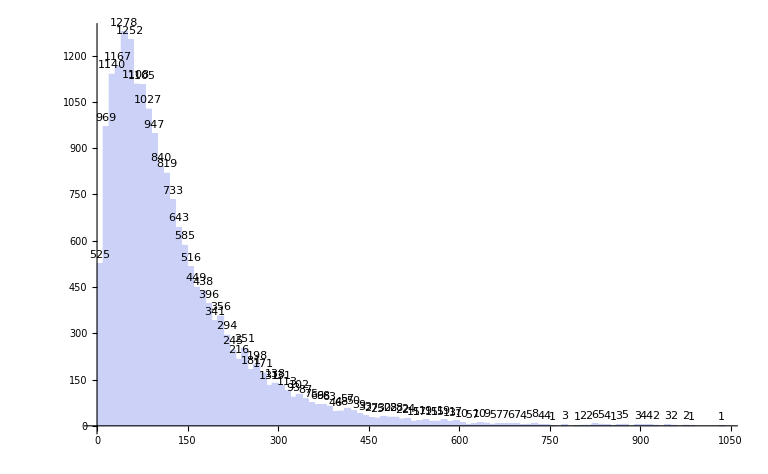

126.981

```mathematica
Histogram[features[[All,3]],LabelingFunction->Above]
N[Mean[features[[All,3]]]]
```

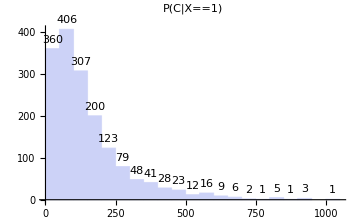
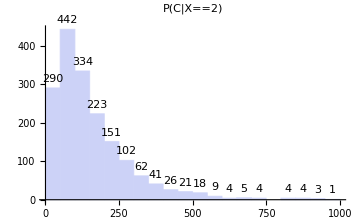
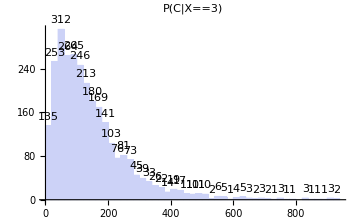
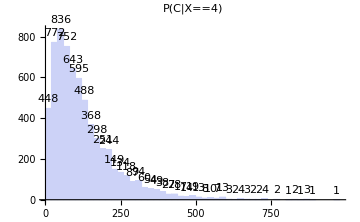
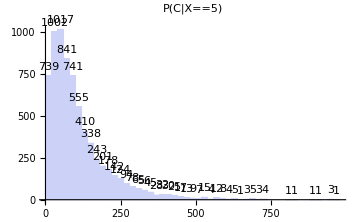

```mathematica
ratings=Range[1,5,1];
Table[
Histogram[Select[features,#[[2]]==r&][[All,3]],LabelingFunction->Above,PlotLabel->P[C|X==r],ImageSize->Medium],
{r,ratings}
]
```

## UCase Count

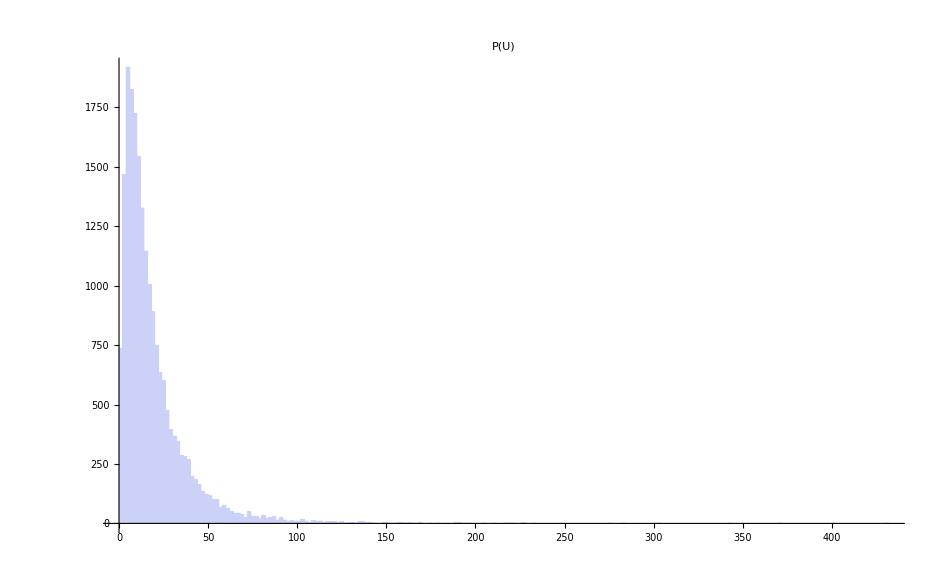

18.5203

```mathematica
Histogram[features[[All,4]],PlotLabel->P[U],ImageSize->Large]
N[Mean[features[[All,4]]]]
```

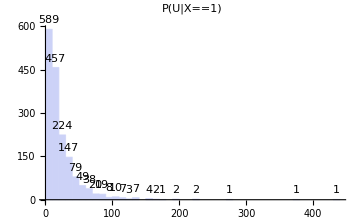
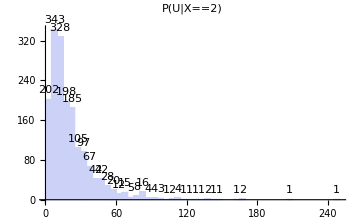
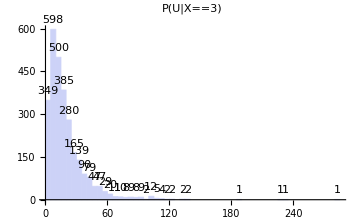
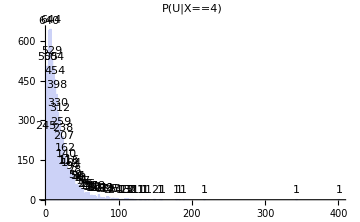
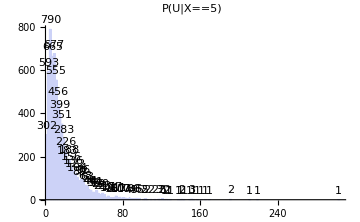

```mathematica
ratings=Range[1,5,1];
Table[
Histogram[Select[features,#[[2]]==r&][[All,4]],LabelingFunction->Above,PlotLabel->P[U|X==r],ImageSize->Medium],
{r,ratings}
]
```

## Prior of Classes

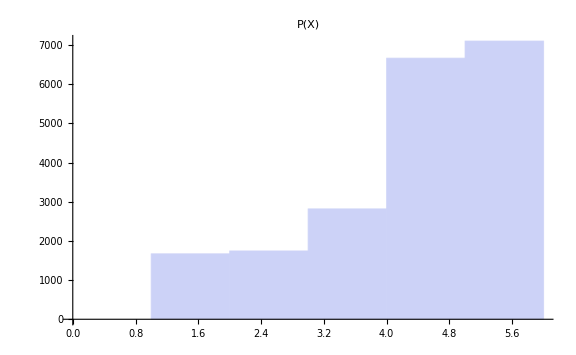

3.78915

```mathematica
Histogram[features[[All,2]],PlotLabel->P[X],ImageSize->Large]
N[Mean[features[[All,2]]]]
```